```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/feng/Library/CloudStorage/GoogleDrive-lyu00145@umn.edu/我的云端硬盘/mathematica/Vector-Like-Fermion

```mathematica
<<CustomTicks`
```

```mathematica
βW=4mW^2/mh^2;βt=4*mt^2/mh^2;βT=4*mT^2/mh^2;
ff[β_]=ArcSin[1/Sqrt[β]]^2;
```

```mathematica
FW=2+3βW+3βW(2-βW)ff[βW];
Ft=3*(2/3)^2(-2βt)(1+(1-βt)ff[βt])(1-sLs);
FT=3*(2/3)^2(-2βT)(1+(1-βT)ff[βT])sLs ;
```

```mathematica
FStot[mT_,sLs_]=(FW+Ft+FT)^2//.{mh->125,mt->173,mW->80.3}//Simplify;
FSgtot[mT_,sLs_]=(Ft+FT)^2//.{mh->125,mt->173,mW->80.3}//Simplify;
```

```mathematica
FSM=(FW+Ft)^2//.{mh->125,mt->173,mW->80.3,sLs->0}//Simplify;
FSMg=Ft^2//.{mh->125,mt->173,mW->80.3,sLs->0}//Simplify;
Rhpp[mT_,sLs_]=Abs[FStot[mT,sLs]/FSM-1];
```

```mathematica
Rhgg[mT_,sLs_]=Abs[FSgtot[mT,sLs]/FSMg-1];
```

```mathematica
((-2βt)(1+(1-βt)ff[βt]))^2/0.344065//.{mh->125,mt->173.}
((-2βt)(1+(1-βt)ff[βt]))^2/0.344065//.{mh->125,mt->17300.}
```

5.50505

5.16701

```mathematica
Assuming[{a0>1},Integrate[(1-4x z)/(1-4x z a0),{x,0,1},{z,0,1-x}]]
```

$Aborted

```mathematica
Assuming[{a0<1},Integrate[(1-4x z)/(1-4x z a0),{x,0,1},{z,0,1-x}]]
```

```mathematica
NIntegrate[(1-4x z)/(1-x z 125^2/173^2),{x,0,1},{z,0,1-x}]
```

0.344065

```mathematica
NIntegrate[(1-4x z)/(1-x z 125^2/5000^2),{x,0,1},{z,0,1-x}]
```

0.333345

```mathematica
aT[mT_,sLs_]=3(-(gw^2 mt^2 sL^2 (mt^2-2 mT^2 Log[mt]-mT^2+2 mT^2 Log[mT]))/(32 π^2 cw^2 MZr^2 (mt^2-mT^2))+(gw^2 sL^4 (mt^4-4 mt^2 mT^2 Log[mt]+4 mt^2 mT^2 Log[mT]-mT^4))/(64 π^2 cw^2 MZr^2 (mt^2-mT^2))//.{sL->√sLs,MZr->gw/cw vev/2}//Simplify)//.{mt->173.,vev->246.};
```

```mathematica
logRegionPlot[rplot_]:=Module[{pts,pgon},pts=Cases[Normal@rplot,Line[a__]:>a,Infinity];
pgon={EdgeForm[],Directive[RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6],Opacity[0.3]],Cases[Normal@rplot,Polygon[_],Infinity]};
ListLogPlot[pts,Joined->True,Frame->True,PlotRange->All,AspectRatio->1,Axes->False,PlotStyle->ColorData[1][1],Epilog->(pgon/. {x_,y_?NumericQ}:>{x,Log@y})]]
```

```mathematica
Rhpp[6000,0.1]
Rhgg[6000,0.1]
```

0.00176232

0.0062237

```mathematica
cleanRegionPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,{__,_Line},Infinity];(*only change*)Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]];
```

```mathematica
Lams[mN_,sLs_]=2(sLs (mN^2-173^2)+173^2)/246.^2;
```

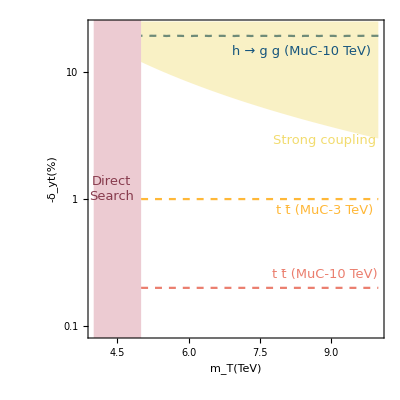

```mathematica
figtot=Show[ContourPlot[{(*aT[1000mN,0.01sLs]==0.1/128,*)Rhgg[1000mN,0.01sLs]==0.012,(*Rhgg[1000mN,0.01sLs]==0.02,*)sLs==1,sLs==0.2(*,aT[1000mN,0.01sLs]==0.1/128*)},{mN,5,10},{sLs,0.09,25},PlotRange->{{4,10},{0.09,23}},ScalingFunctions->{None,"Log"},FrameTicksStyle->Directive[Black,15],ContourStyle->{(*Directive[Black],*)Directive[Dashed,ColorData[colorselecitonumber][7]],(*Directive[Dashed,ColorData[colorselecitonumber][3]],*)(*Directive[ColorData[colorselecitonumber][9]],*)Directive[Dashed,ColorData[colorselecitonumber][2]],Directive[Dashed,ColorData[colorselecitonumber][1]],Directive[Dashed,ColorData[colorselecitonumber][4]]},Frame->True,BaseStyle->{FontFamily->"Times"},FrameLabel->{{Style["-δ_yt(%)",Black,15],None},{Style["m_T(TeV)",Black,15],None}},FrameTicksStyle->Directive[Black,13],Epilog->{Inset[Style["h → g g (MuC-10 TeV)",ColorData[colorselecitonumber][7],13],Scaled[{0.72,0.9}]],Inset[Style["t t̄ (MuC-10 TeV)",ColorData[colorselecitonumber][1],13],Scaled[{0.8,0.2}]],Inset[Style["t t̄ (MuC-3 TeV)",ColorData[colorselecitonumber][2],13],Scaled[{0.8,0.4}]],
Inset[Style["Strong coupling",ColorData[colorselecitonumber][13],13],Scaled[{0.8,0.62}]],Inset[Style["Direct\nSearch",ColorData[colorselecitonumber][9],13],Scaled[{0.08,0.47}]]}],Graphics[{Opacity[0.7,ColorData[colorselecitonumber][10]],Rectangle[{4,-3},{5,4}]},Frame->True,PlotRange->{{4,10},All}],cleanRegionPlot@RegionPlot[Lams[1000mN,0.01sLs]>10^2,{mN,5,10},{sLs,0.09,25},ScalingFunctions->{None,"Log"},BoundaryStyle->None,PlotStyle->Opacity[0.4,ColorData[colorselecitonumber][13]]]]
```

```mathematica
Export["VLQ_para.pdf",figtot,ImageResolution->500]
```

VLQ_para.pdf